# QNM Schwarzchild-de Sitter: de Sitter Limit Scenario

Copyright: Yi Zhou; Rodrigo Panosso Macedo (2025)
ArXiv-gr-qc: 2507.05370
PRD       (2025)

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
(*$Assumptions={M>0}*)
```

/Users/qtc325/Trabalhos/HypeBHPT/SdS_QNM

## SdS Spacetime: Functions and Hyperboloidal approach

## Horizon parametrisation

```mathematica
rh= rΛ*η;
ro=- rΛ/ο;
Subsο=Solve[{ro+rh+rΛ==0},ο][[1]]

λ= rΛ; (* Hyperboloidal Lenght scale*)
```

{ο→1/(1+η)}

## Radial compactification

```mathematica
func$r[σ_]:= λ/σ (ρρ0 + ρρ1 * σ)
Subsρ=Solve[    {func$r[σSing]==0, func$r[1]==rΛ},{ρρ0,ρρ1}     ] [[1]]
```

{ρρ0→σSing/(-1+σSing),ρρ1→-1/(-1+σSing)}

```mathematica
ρ1=ρρ1/.Subsρ
ρ0=ρρ0/.Subsρ
rFunc[σ_]:=  λ/σ (ρ0 + ρ1 * σ)

SubsσH=Solve[rFunc[σH]==rh,σH][[1]]

σΛ=1
σh=σH/.SubsσH
```

-1/(-1+σSing)

σSing/(-1+σSing)

{σH→σSing/(1-η+η σSing)}

1

σSing/(1-η+η σSing)

## Physical Potential

### Line element

```mathematica
f= -r^2 Λ/3*(1-rh/r)(1-rΛ/r)(1-ro/r)
f$par=1-2 MM/r - Λ*r^2/3


diff$f=Collect[f-f$par/.Subsο,r]
Coef0=Coefficient[diff$f,r,0]
Coefm1=Coefficient[diff$f,r,-1]
Coefp1=Coefficient[diff$f,r,1]

SubsΛM=Solve[{Coef0==0,Coefm1==0},{Λ,MM}][[1]]//FullSimplify
```

-1/3 r^2 (1-rΛ/r) (1-(rΛ η)/r) Λ (1+rΛ/(r ο))

1-(2 MM)/r-(r^2 Λ)/3

-1-1/3 rΛ^2 η Λ+1/3 rΛ^2 (1+η) Λ+1/3 rΛ^2 η (1+η) Λ+r ((rΛ Λ)/3+(rΛ η Λ)/3-1/3 rΛ (1+η) Λ)+(2 MM-1/3 rΛ^3 η (1+η) Λ)/r

-1-1/3 rΛ^2 η Λ+1/3 rΛ^2 (1+η) Λ+1/3 rΛ^2 η (1+η) Λ

2 MM-1/3 rΛ^3 η (1+η) Λ

(rΛ Λ)/3+(rΛ η Λ)/3-1/3 rΛ (1+η) Λ

{Λ→3/(rΛ^2 (1+η+η^2)),MM→(rΛ η (1+η))/(2 (1+η+η^2))}

```mathematica
(*EXERCISE: Derive the wave equation for SdS in (t,r) coordinates. Find what is the a generic spherically symmetric spacetime with a(r)=b(r)=f(r) scalar potential*)
```

```mathematica
V$of$r = f*( l*(l+1)/r^2 + D[f,r]/r)/.SubsΛM/.Subsο//FullSimplify;

V= V$of$r/.r->rFunc[σ]//FullSimplify//FullSimplify
```

-1/(rΛ^2 (1+η+η^2)^2 (σ-σSing)^4)(-1+σ) σ (-η (1+η)-(2 (σ-σSing)^3)/(σ^3 (-1+σSing)^3)+(l (1+l) (1+η+η^2) (σ-σSing))/(σ (-1+σSing))) (-1+σSing) σSing (σSing+σ (-2+η (-1+σSing)+σSing)) (σSing+σ (-1+η-η σSing))

## Hyperboloidal functions

### Dimensionless Tortoise Coordinate

```mathematica
xh = (rΛ η Log[-σ+σSing/(1-η+η σSing)])/((-2+(3 (1+η))/(1+η+η^2)) λ);
xΛ = (rΛ Log[-1+σ])/((1-3/(1+η+η^2)) λ);
xo = (rΛ (1+η) (1+η+η^2) Log[σ+σSing/(-2+η (-1+σSing)+σSing)])/((2+η) (1+2 η) λ);
x = xh + xΛ + xo

dx$dσ=D[x,σ]//FullSimplify
```

Log[-1+σ]/(1-3/(1+η+η^2))+((1+η) (1+η+η^2) Log[σ+σSing/(-2+η (-1+σSing)+σSing)])/((2+η) (1+2 η))+(η Log[-σ+σSing/(1-η+η σSing)])/(-2+(3 (1+η))/(1+η+η^2))

-((1+η+η^2) (σ-σSing) (-1+σSing))/((-1+σ) (σ+η σ (-1+σSing)-σSing) (σSing+σ (-2+η (-1+σSing)+σSing)))

### Height Function

```mathematica
H = xh - xΛ + xo
dH$dσ=D[H,σ]//FullSimplify
```

-Log[-1+σ]/(1-3/(1+η+η^2))+((1+η) (1+η+η^2) Log[σ+σSing/(-2+η (-1+σSing)+σSing)])/((2+η) (1+2 η))+(η Log[-σ+σSing/(1-η+η σSing)])/(-2+(3 (1+η))/(1+η+η^2))

(1+η+η^2) (-1/((-2+η+η^2) (-1+σ))-η/((1+η-2 η^2) (-σ+σSing/(1+η (-1+σSing))))+(1+η)/((2+η) (1+2 η) (σ+σSing/(-2+η (-1+σSing)+σSing))))

```mathematica
p=-1/dx$dσ//FullSimplify

γ=p * dH$dσ//FullSimplify
w=(1- γ^2)/p//FullSimplify


Pot=λ^2/p * V//FullSimplify
```

((-1+σ) (σ+η σ (-1+σSing)-σSing) (σSing+σ (-2+η (-1+σSing)+σSing)))/((1+η+η^2) (σ-σSing) (-1+σSing))

(2 σSing+η (1+η) (-1+σSing) σSing-2 σ^2 (1+η (-1+σSing)) (-2+η (-1+σSing)+σSing)+σ (-2+η+η^2-(4+η+η^2) σSing+2 σSing^2))/((-1+η) (2+η) (σ-σSing) (-1+σSing))

(4 (1+η+η^2) (-σ (1+η (-1+σSing)) (-2+η (-1+σSing)+σSing)+σSing (-2-η (1+η) (-1+σSing)+σSing)))/((-2+η+η^2)^2 (σ-σSing) (-1+σSing))

-(σ (-η (1+η)-(2 (σ-σSing)^3)/(σ^3 (-1+σSing)^3)+(l (1+l) (1+η+η^2) (σ-σSing))/(σ (-1+σSing))) (-1+σSing)^2 σSing (σSing+σ (-1+η-η σSing)))/((1+η+η^2) (σ-σSing)^3 (σ+η σ (-1+σSing)-σSing))

```mathematica
Pot//FullSimplify
(σSing+σ (-1+η-η σSing))/(σ+η σ (-1+σSing)-σSing)//FullSimplify
σh
```

-(σ (-η (1+η)-(2 (σ-σSing)^3)/(σ^3 (-1+σSing)^3)+(l (1+l) (1+η+η^2) (σ-σSing))/(σ (-1+σSing))) (-1+σSing)^2 σSing (σSing+σ (-1+η-η σSing)))/((1+η+η^2) (σ-σSing)^3 (σ+η σ (-1+σSing)-σSing))

-1

σSing/(1-η+η σSing)

#### Asymptoptic behaviour potential

```mathematica
Series[Pot, {σ,0,1}]
```

-(2 σSing)/(((1+η+η^2) (-1+σSing)) σ^2)+((l+l^2) (-1+σSing))/σSing+((-1+σSing) (2 l+2 l^2-η+2 l η+2 l^2 η-η^2+2 l η^2+2 l^2 η^2+η σSing+η^2 σSing) σ)/((1+η+η^2) σSing^2)+O[σ]^2

```mathematica
pdS=p/.σSing->2/.η->0//FullSimplify
γdS=γ/.σSing->2/.η->0//FullSimplify
wdS=w/.σSing->2/.η->0//FullSimplify
PotdS=Pot/.σSing->2/.η->0//FullSimplify
```

2 (-1+σ)

1

0

(2 l (1+l))/(-2+σ)^2-4/σ^2

## QNM Eigenvalue Solver

## Physical Parameters

```mathematica
spin=0; (*SCALAR PERTURBATIONS*) (*NOTE: SO FAR, ONLY POTENTIAL FOR SCALAR FIELD IS IMPLEMENTED*)
l=2; (*ANGULAR MODE*)
η=0; (*de Sitter scale*)
σSing=2; (*de Sitter scale*)
```

## Discrete Functions and Matrices

### Spectral Routines

#### Chebyshev Coefficients

```mathematica
ChebGaussCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[ Cos[Pi*(j+1/2)/(Nf+1)] ,Prec];

c=Table[  2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,0,Nf}]  /nf        ,{m,0,Nf}]
];

ChebLobattoCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[Cos[j π/Nf],Prec];

c=Table[  ( 2-KroneckerDelta[m,Nf]) /(2Nf) (  f[[1]]+(-1)^m f[[nf]] + 2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,1,Nf-1}]  )        ,{m,0,Nf}]
];
```

#### Spectral Differentiation matrices

```mathematica
DiffMatrix[a_,b_,Nz_,Prec_]:=Module[
{k,i,j,dx, Δ,Dy},

k[i_]:=If[i*(i-Nz)==0, 2,1];
dx[i_,j_]:=If[i!=j,
k[i]*(-1)^(i-j)/(k[j]*(x[i,Nz]-x[j,Nz])),
0
];
Δ=b-a;
Dy=N[2/Δ * Table[dx[i,j], {i,0,Nz}, {j,0,Nz}],Prec ];

For[i=0, i<=Nz, i++,
Dy[[i+1,i+1]]= -Sum[ Dy[[i+1,j+1]], {j,0,Nz} ];
];
Dy
]
```

#### Chebyshev Interpolation

```mathematica
ChebInterpolation[c_,a_,b_,x_]:=Module[
{nc, Nc},
nc=Length@c;
Nc=nc-1;

y=(2 x-(a+b))/(b-a);

c[[1]]/2+Sum[c[[i+1]]*ChebyshevT[i,y],{i,1,Nc}]
];

ChebyLobattoInterpolationVector[xl_,Nl_,xα_,Prec]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα]/(Nl),{j,1,Nl}]
]
],
{l,0,Nl}
]

];

ChebyLobattoInterpolationMatrix[xl_,Nl_,xα_,Nα_,Prec]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα[[α+1]]]/(Nl),{j,1,Nl}]
]
],
{α,0,Nα},{l,0,Nl}
]

]
```

#### Chebyshev Integration

```mathematica
DefiniteIntegral[c_,a_,b_]:=Module[
{kf,nc,Nc, Int},
nc=Length@c;
Nc=nc-1;
kf=Floor[Nc/2];
Int=c[[1]]- 2Sum[c[[2 k +1]]/(4 k ^2 -1),{k,1,kf}];
(b-a)*Int/2
];

ChebyLobattoHilbertIntegration[z_,Nz_,Prec_]:=Module[
{i,j},
Table[
If[i!=j,
0,
If[i==0 || i==Nz,
(1/Nz - Sum[(2-KroneckerDelta[2k,Nz])/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}]),
(2/Nz - 2Sum[(2-KroneckerDelta[2k,Nz])*ChebyshevT[2k,z[[i+1]]]/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}])
]
],
 {i,0,Nz}, {j,0,Nz}
]
]
```

### Numerical parameters

```mathematica
Prec=10*MachinePrecision;
x=.
z0=σΛ;
z1=σh;

Δz=z1-z0;

Nz=100;
nz=Nz+1; (*Total number of points*)

x[i_,Nz_]:=Cos[(π i)/Nz];
(*x[i_,Nz_]:=Cos[(π (i+1/2))/(Nz+1)];*)

χ=N[Table[x[i,Nz],{i,0,Nz}],Prec];
ZeroArray=ConstantArray[0,nz];
(*z=N[Table[z0+1/2 Δz (1+x[i,Nz]),{i,0,Nz}],Prec];

ListPlot[Transpose@{z,ZeroArray}, AxesLabel->{"σ",""}]*)
```

#### AnMR Parameter

```mathematica
xb=1;
κ=0;(*1+Abs[Log10[η]]*)
If[κ==0,
(*CONDITION WHEN κ==0*)
X=χ;
z=N[z0+1/2 Δz*(1+X),Prec]
,
(*CONDITION WHEN κ!=0*)
X=N[xb*(1-2*Sinh[κ*(1-xb*χ)]/Sinh[2*κ]),Prec];
z=N[z0+1/2 Δz*(1+X),Prec]
];

(*ListPlot[{Transpose@{χ,ZeroArray},Transpose@{X,ZeroArray+0.01}}, PlotRange->{-0.5,0.5}]*)
```

### Discrete Functions

```mathematica
pVec=pdS*(2-σ)^2/.σ->z;
dpVec=D[pdS,σ]*(2-σ)^2/.σ->z;
PotVec=Limit[PotdS*(2-σ)^2,σ->z];
γVec=γdS*(2-σ)^2/.σ->z;
dγVec=D[γdS,σ]*(2-σ)^2/.σ->z;

wVec=wdS*(2-σ)^2/.σ->z;
```

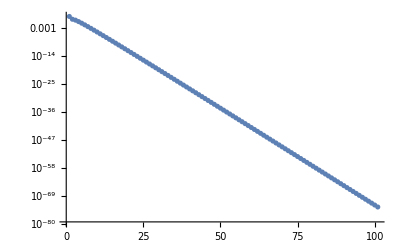

```mathematica
cPot=ChebLobattoCoefficients[PotVec,Prec];
ListLogPlot[Abs@cPot]
```

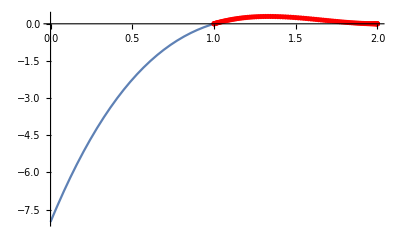

```mathematica
Plot$p=Plot[pdS*(2-σ)^2,{σ,0,σSing}];
Plot$pVec=ListPlot[Transpose@{z,pVec}, PlotStyle->Red];
Show[Plot$p,Plot$pVec]
```

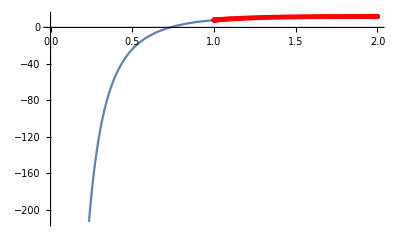

```mathematica
Plot$Pot=Plot[PotdS*(2-σ)^2,{σ,0,σSing}];
Plot$PotVec=ListPlot[Transpose@{z,PotVec}, PlotStyle->Red];
Show[Plot$Pot,Plot$PotVec]
```

### Differentiation Matrices

[Calculating the discrete representation of the derivate operator δσ ---> Dσ]

#### Create directory to store differentiation matrices

```mathematica
DirName$Matrices="OperatorMatrix";
If[!DirectoryQ[DirName$Matrices],CreateDirectory[DirName$Matrices]]
```

#### Create or Load Matrices

```mathematica
fn$Dχ="OperatorMatrix/Dchi_"<>"N_"<>ToString[Nz]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_"<>"N_"<>ToString[Nz]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dχ=FileExistsQ[fn$Dχ];
check$D2χ=FileExistsQ[fn$D2χ];

If[!check$Dχ || !check$D2χ, 
Print["Calculating Differentiation Matrices"];

Dχ=DiffMatrix[-1,1,Nz,Prec]; 
D2χ=Dχ . Dχ;

Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ],"Table"];,

Print["Loading Differentiation Matrices"];
Dχ=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id=IdentityMatrix[Nz+1];
Zero=ConstantArray[0,{Nz+1,Nz+1}];
```

Loading Differentiation Matrices

#### Analytical Mesh Refiniment

```mathematica
If[κ==0,
(*CONDITION κ ==0*)
Dx=Dχ;
D2x=D2χ
,
(*CONDITION κ != 0*)
J=N[ 2*κ*Cosh[κ*(1-χ*xb)]/Sinh[2*κ],Prec];
J2=N[ -2*κ^2*xb*Sinh[κ*(1-χ*xb)]/Sinh[2*κ],Prec];

Dx = N[Dχ/J,Prec];
D2x = N[(D2χ - J2*Dx)/J^2,Prec]
];
```

#### Map into σ ∈ [0,σh]

```mathematica
Dσ=2/Δz Dx;
D2σ=(2/Δz)^2 D2x;
```

## QNM Eigenvalue Problem

-s^2 w + L1[ϕ] + s * L2 [ϕ] = 0
if w = 0
L1[ϕ] = - s * L2 [ϕ]  (Generalised Eigenvalue Solver)

### Discrete ODE operators

```mathematica
L1=pVec*D2σ + dpVec*Dσ - PotVec*Id;
L2=2*γVec*Dσ + dγVec*Id;

L$lhs = L1;
L$rhs = -L2;

(*L=N[ArrayFlatten[{
{Zero,Id} , 
{L1/wVec,L2/wVec} 
}
],
Prec];*)
```

### Solve Eigenvalue

```mathematica
Print["Calculating QNM"];
EigenSol=Eigenvalues[{L$lhs,L$rhs}];
Print["Done"];
```

Calculating QNM

Done

#### Re-scale Laplace to Fourier

```mathematica
ω=Delete[-I*EigenSol,1];
```

#### Filter discrete from continuous spectra

```mathematica
PosQNM=Position[EigenSol,x_/;Im@x!=0]//Flatten;

nQNM=Length@PosQNM;
ω$QNM=Table[ω[[PosQNM[[i]]]],{i,1,nQNM}];

PosBranch=Position[EigenSol,x_/;Im@x==0]//Flatten;
nBranch=Length@PosBranch-1;
ω$BranchCut=Table[ω[[PosBranch[[i]]]],{i,1,nBranch}];

QNMData=Table[{Re@ω$QNM[[iqnm]],Im@ω$QNM[[iqnm]]},{iqnm,1,Length@ω$QNM}];
BranchCutData=Table[{Re@ω$BranchCut[[iqnm]],Im@ω$BranchCut[[iqnm]]},{iqnm,1,nBranch}];
```

#### Plot

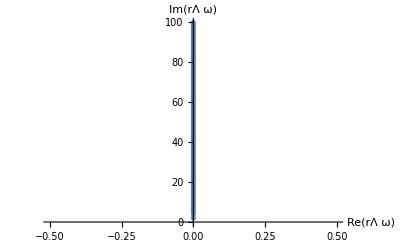

```mathematica
ListPlot[BranchCutData,
AxesLabel->{"Re("<>ToString[λ]<>" ω)","Im("<>ToString[λ]<>" ω)"}, PlotRange->{{-0.5, 0.5},{0,100}}]
```

#### Individual Overtones

```mathematica
N[ω$BranchCut[[-1]],20]
N[ω$BranchCut[[-2]],20]

N[ω$BranchCut[[-3]],20]
N[ω$BranchCut[[-4]],20]

N[ω$BranchCut[[-5]],20]
N[ω$BranchCut[[-6]],20]
```

Fundamental mode n = 0

2. ⅈ

4. ⅈ

5. ⅈ

6. ⅈ

7. ⅈ

8. ⅈ

### Export Data

```mathematica
(*DirName$Data="Data/SdS_dSLimit";*)
DirName$Data="Data/dSLimit_Continuous";
If[!DirectoryQ[DirName$Data],CreateDirectory[DirName$Data]]
```

```mathematica
Print["Export Data"];
fn=DirName$Data<>"/QNM_N_"<>ToString[Nz]<>"_eta_"<>ToString[N[η,3]]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

Export[fn,N[QNMData,Prec],"Table"]
fn=DirName$Data<>"/Branch_N_"<>ToString[Nz]<>"_eta_"<>ToString[N[η,3]]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
Export[fn,N[BranchCutData,Prec],"Table"]

Print["Done"]
```

Export Data

Data/dSLimit_Continuous/QNM_N_100_eta_0_l2_spin0_Prec_159.dat

Data/dSLimit_Continuous/Branch_N_100_eta_0_l2_spin0_Prec_159.dat

Done